```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/blogit"]
```

/Users/pjoot/project/figures/blogit

```mathematica
<<MaTeX`

(*See MathematicaColorToLatexRGB.nb for color mapping logic.*)
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 16]
```

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{xcolor,txfonts},\definecolor{BlueDarker}{HTML}{0000AA},\definecolor{RedDarker}{HTML}{AA0000},\definecolor{PurpleDarker}{HTML}{550055},\definecolor{OrangeDarker}{HTML}{AA5500},\definecolor{GreenDarker}{HTML}{00AA00}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→16,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

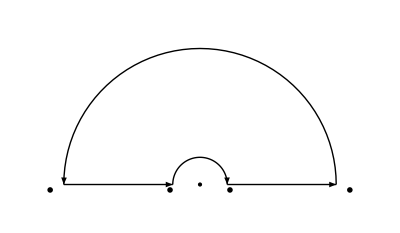

```mathematica
ClearAll[R, lineArrow, rl, rh, xrange1, xrange2, semicircleArrow, weightedSincFig1]
R=5; 
r = 1;
xrange1 = {{-R,0},{-r, 0}};
xrange2 = {{r,0},{R, 0}};
lineArrow=Graphics[{
Thick,Arrow[xrange1],Arrow[xrange2],
Text[MaTeX["-R"], {-1.1 R, -0.2}],
Text[MaTeX["R"], {1.1 R, -0.2}],
Text[MaTeX["-\\rho"], {-1.1 r, -0.2}],
Text[MaTeX["\\rho"], {1.1 r, -0.2}],
PointSize -> Large,
Point[{0,0}]
}];

(*Semicircular arc with arrow*)
rl[s_] := Pi (1-UnitStep[s]);
rh[s_] := Pi UnitStep[s];

semicircleArrow[a_,s_:1]:=Graphics[{Thick,Arrow[Table[{a Cos[t],a Sin[t]},{t,rl[s],rh[s],s Pi/50}]]}]

weightedSincFig1 = Show[lineArrow,semicircleArrow[R, 1],semicircleArrow[r, -1],AspectRatio->Automatic,PlotRange->{{-R-1,R+1},{-1,R+1}},Axes->False,Ticks->None,Frame->False]
```

```mathematica
peeters`exportForLatex["weightedSincFig1",weightedSincFig1]
```

{weightedSincFig1.eps,weightedSincFig1pn.png}